```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCTools`"]];
<<GDCAnalysis3`
<<GDCTools`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCTools.m

```mathematica
(* CROSS CHECK --- S0 --- DLB *)
PosFileIn="/home/carla/GDC/POS/gdc_pos_S2.txt";
chPoolIn=Get["/home/carla/GDC/CH_Pool/CH_Pool_Simp.txt"];
TauIn=Get["/home/carla/GDC/TAU2/GDC_Tau_Simplified_S2.txt"];
SigIn=Get["/home/carla/GDC/SIG2/GDC_Sigma_2_S2.txt"];

persListe={17,17,17};
```

```mathematica
(*confCHPoolFunc[sigFI_,tauFI_,posFI_, chP_, persL_, revM_, modAll_]*)
dataEx=Map[confCHPoolFunc[SigIn,TauIn,PosFileIn, #, persListe, "AR", "ALL"]&,chPoolIn];
```

```mathematica
dataEx[[1,1]]
Length[dataEx[[1,1]]]
dataEx[[All,2,1]][[1;;3]]
```

{0.00146843,1,681}

3

{0.00111543,0.00105967,0.00105967}

```mathematica
dataExdoj=Map[confCHPoolFunc[SigIn,TauIn,PosFileIn, #, persListe, "AR", "DOJ"]&,chPoolIn];
```

```mathematica
dataExdoj[[1,1]]
Length[dataExdoj[[1,1]]]
dataExdoj[[All,1]][[1;;3]]
```

0.00146843

0

{0.00146843,0.00146843,0.00146843}

```mathematica
Range[0]
```

{}

```mathematica
doj=minmaxFunc[dataEx[[All,1,1]], chPoolIn];
```

```mathematica
(*
dataEx[[All,2,1]]
minmaxFunc[dataEx[[All,1,1]], chPoolIn]*)
dataAll=Map[minmaxFunc[dataEx[[All,#,1]], chPoolIn]&,Range[3]];
```

```mathematica
dataAll[[3,3]]
```

{0.612392,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.680997,0.612392,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.612392,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,-1,0.612392,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.612392,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,-1,0.612392,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.564498,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,-1,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,-1,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,0.094821,-1,0.094821,0.094821,0.094821,0.094821,-1,0.094821,0.094821,0.094821,0.094821,-1,0.094821,0.094821,0.094821,0.094821,-1,0.094821,-1,-1,-1,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,-1,-1,-1,0.266833,0.0815745,0.0815745,0.0815745,-0.00188438,0.0815745,-0.00188438,-0.00188438,-1,-1,-1,-1,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-0.00188438,-1,-1,-1,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,0.266833,0.0815745,-0.00188438,-0.00188438,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,-0.00188438,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.67378,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,-1,0.539773,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.603987,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,-1,0.603987,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,0.555341,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,-1,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,-1,0.0815745,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,-1,0.266833,-0.00188438,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,0.0815745,-0.00188438,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,-1,0.0815745,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,-1,-1,0.0815745,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745,0.0815745,0.0815745,0.0815745,-1,0.0815745}

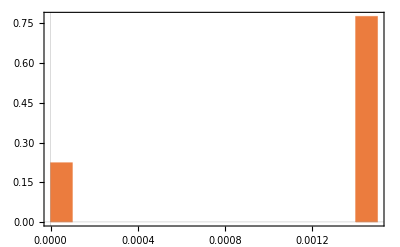

```mathematica
doj=dataEx[[All,1,1]];
dojHist=Histogram[doj,{0.0001},"Probability",PlotTheme->"Scientific"]
```

```mathematica
dojDataOut=minmaxFunc[doj, chPoolIn];
```

```mathematica
SetDirectory["/home/carla/GDC/CH_Pool/DOJ"];
Put[dojDataOut,"CH_Pool_DOJ.txt"]
```